# Métodos numéricos: Hoja 2

## Ejercicio 1:

Primero hemos calculado f(0.84) a partir de la tabla inicial, utilizando el método de interpolación de Lagrange. Después, hemos reconstruido la función con un mallado de 50 puntos en el intervalo [0,3.5], interpolando cada uno de los puntos del mallado usando el mismo método y representado en Mathematica, como sigue a continuación:

```mathematica
SetDirectory [NotebookDirectory[]];
datos=Import["datos.txt","Table"];
datosmallado=Import["datosmallado.txt","Table"];
puntos=ListPlot[datos,PlotStyle-> {PointSize[0.025],RGBColor[1,0,0]}]
puntosmallado=ListPlot[datosmallado,PlotStyle-> {PointSize[0.01],RGBColor[0,0,1]}]
f[x_]:=InterpolatingPolynomial[datos,x]
g=Plot[f[x],{x,0,3.5}]
Show[puntos,puntosmallado,g]
```

Se muestra a continuación los nodos originales:

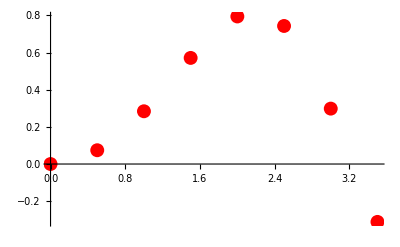

Nuestra representación obtenida de la interpolación con 50 puntos de mallado es de la forma:

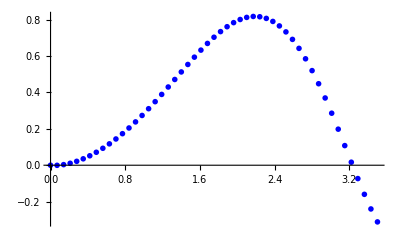

La interpolación que se muestra es la obtenido con Mathematica:

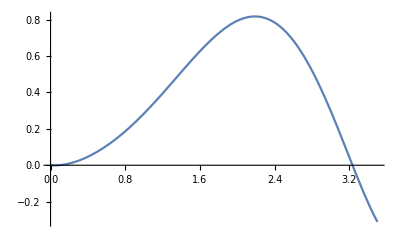

Esta es la representación conjunta de los nodos originales y la interpolación calculada en todos los nodos del mallado:

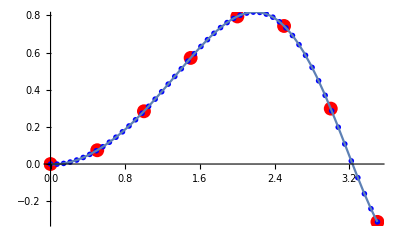

Vemos que la reconstrucción de la función se corresponde muy bien con los puntos iniciales de la tabla.

## Ejercicio 2:

Se dibuja en Mathematica: los puntos utilizados en la interpolación, la aproximación obtenida en Fortran y por último ambas representaciones en la misma gráfica.

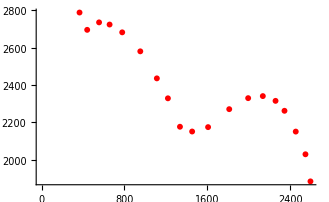

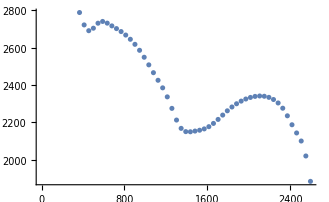

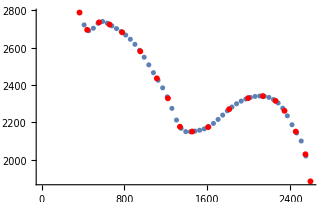

```mathematica
SetDirectory[NotebookDirectory[]];
f=Import ["spoutput.txt","Table"];
b=Import["spdata.txt","Table"];
B=ListPlot[b,PlotStyle->Red]
F=ListPlot[f]
Show[F,B]
```

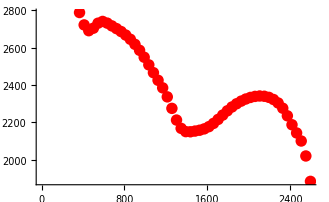

A continuación se muestra la función interpoladora que crea Mathematica .Se comprueba que nuestro resultado en Fortran y esta son muy parecidas entre sí:

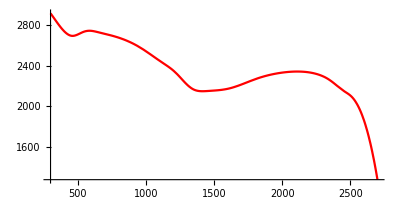

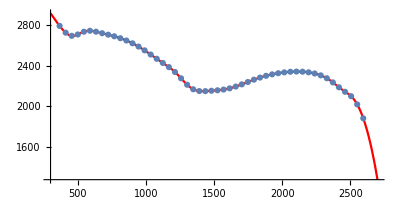

```mathematica
interpolacion=Interpolation[f,Method->"Spline"];
interpolacion=Plot[interpolacion[x],{x,300,2700},PlotStyle->Red,AspectRatio->1/2]
Show[interpolacion,F]
```

A continuación vamos a calcular el polinomio interpolador para la cebra y comentar su resultado, tal y como pide el apartado 2.2.d.

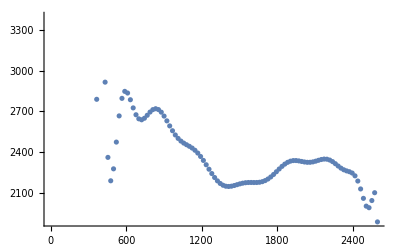

```mathematica
SetDirectory[NotebookDirectory[]];
t=Import ["lagrangeoutput.txt","Table"];
f=Import ["spoutput.txt","Table"];
F=ListPlot[f,PlotStyle->Red,AspectRatio->1/2];
T=ListPlot[t];
```

Se nuestra en la gráfica el polinomio interpolador mediante Lagrange para 100 puntos.

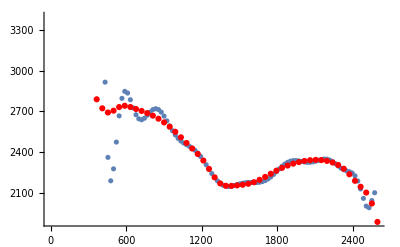

```mathematica
Show[T,F]
```

Representamos nuestro resultado obtenido mediante splines y el polinomio interpolador. En este caso último caso no se consigue representar la función correctamente. Si comparamos con la gráfica de la silueta de la cebra vemos que ambas son muy distintas. Esto es debido a que las interpolaciones polinómicas no son adecuadas para funciones con cambios bruscos.